# Surface Energy Density and its Effects on Small Particles: Part 1

In this chapter, we investigate the excess energy associated with surfaces. We will show that surface tension tends to reduce the lattice constant of small particles and show how to calculate an orientation-dependent surface free energy density.  Finally, we will look at some numerical methods to speed up the computation of equilibria.

We will use a simple model for interactions: Lennard-Jones.  Examples for ionic bonding will be treated in a separate chapter.

#### Because the Lennard-Jones potential has a hexagonal lattice as its minimizing structure, we will create a hexagonal lattice and then create circular particles

We will use the normalized form of the Lennard - Jones potential

We will pick the lattice constant in our work to be 1 rMin, and all energies will be measured in units of eMin.

```mathematica
hexLatticeVectors = {{0,1},{(√3)/2,1/2}}
```

Creating lattice points that will be used to carve out a circulate particle.

```mathematica
latticePoints = #.hexLatticeVectors&/@N@Tuples[N@Range[-60,60],2];
```

For example

```mathematica
With[
{particle = Select[Norm[#]<50&][latticePoints]},
Graphics[{Circle[#,1/2]&/@particle},ImageSize->Large]
]
```

Note: We will use the words “particle” to describe an ensemble of “atoms”.

We can make round particles up to about size 50 with the part of the lattice we chose.

```mathematica
roundParticle[radius_,latticePoints_]:= Select[Norm[#]<radius&][latticePoints]
```

#### Computing the energy of a particle: Using Matrices to simplify and speed up computation:

Each entry {i,j}  in the DistanceMatrix is the distance between the i^thand j^th atom.  To compute terms like 1/r^6 for all the atoms, we can just do this: 1/DistanceMatrix^6. It’s fast and readable.

However, there are zeroes along the diagonal of the DistanceMatrix (i.e., the distance of a particle to itself is 0).

To avoid division by zero, an identity matrix is added to the DistanceMatrix.  Those additional terms are subtracted at the end

```mathematica
lennardJonesTotalEnergyPerParticle[positions_]:=
Block[{augmentedDistanceMatrix= DistanceMatrix[positions, DistanceFunction->EuclideanDistance]+ IdentityMatrix[Length[positions]],
pairEnergies,
energiesPerParticle},
pairEnergies = 1/augmentedDistanceMatrix^12- 2/augmentedDistanceMatrix^6;
energiesPerParticle =( Total[pairEnergies]/2 ) + 1/2
]
```

#### For a particle of size 20, here is the range of energies:

```mathematica
{eMin,eMax}=MinMax[lennardJonesTotalEnergyPerParticle[roundParticle[20,latticePoints]]]
```

```mathematica
Histogram[lennardJonesTotalEnergyPerParticle[roundParticle[20,latticePoints]],{.05},Frame->True,FrameLabel->{"Particle Energy","Number of Particles with Energy"},
ImageSize->Large]
```

#### Here is a function to color particles according to their energy. We rescale the energies to lie between 0 and 1, and then raise the result to the power or 1/4. This gives more contrast to the lower energy part of the distribution

```mathematica
energyColor[energy_,{eMin_:(-3.37), eMax_(-1.68)}]:= ColorData["DarkRainbow"][
(Rescale[Clip[energy,{eMin,eMax}],{eMin,eMax},{0,1}])^(.25)]
```

```mathematica
energyColor[#,{eMin,eMax}]&/@Range[eMin,eMax,(eMax-eMin)/24]
```

```mathematica
particleGraphic[positions_,{ eMin_:eMin,eMax_:eMax}]:= MapThread[{energyColor[#1,{eMin,eMax}],Disk[#2,1/2]}&,{lennardJonesTotalEnergyPerParticle[positions],positions}]
```

For example

```mathematica
GraphicsRow[
Graphics[particleGraphic[roundParticle[#,latticePoints]]]&/@{5,10,20}]
```

#### Compute excess energy due to surface

We will compute the Lennard-Jones total energy of  particles for a number of different radii.  Then we will try to extract the excess energy due to a surface.

To simplify things, let’s precompute the atom positions in round particles for a bunch of radii.

```mathematica
particles = <| # -> roundParticle[#,N[latticePoints]]&/@Range[5,50] |>;
```

For example:

```mathematica
Graphics[
particleGraphic[particles[36]]
]
```

We can just sum all the individual atom energies to obtain the total energy of the particle.

```mathematica
totalLennardJonesEnergy[positions_]:=Total[lennardJonesTotalEnergyPerParticle[positions]]
```

#### Here is an example for a particle of radius 5 diameters:

```mathematica
AbsoluteTiming[
totalLennardJonesEnergy[particles[5]]
]
```

{0.013285,-245.296}

#### This is a case were exact computation is going to take a long time clearing fractions and what-not. Numerical calculations are going to be faster. Nevertheless, the next computation will take about 20 seconds:

```mathematica
AbsoluteTiming[
totalLennardJonesEnergy[N@particles[5]]
]
```

```mathematica
energyData=Block[{totalEnergy =totalLennardJonesEnergy[#]},
<|"Total Energy"-> totalEnergy, "Average Energy"-> totalEnergy/Length[#]|>]&/@particles
```

```mathematica
totalEnergyPlot =
ListPlot[energyData[[All,"Total Energy"]],Frame->True,FrameLabel->{"Particle Radius","Total Energy"},ImageSize->Large,
PlotLabel-> "Total Energy per Round Particle",BaseStyle->{FontSize->16}]
```

Remember, the bonding energy (in normalized units) is -1.  Without a surface, we would expect the total energy to decrease linearly with the number of particles

#### Average Energy per particle:

```mathematica
ListPlot[energyData[[All,"Average Energy"]],Frame->True,FrameLabel->{"Particle Radius","Average Energy"},ImageSize->Large,
PlotLabel-> "Average Energy per Round Particle",BaseStyle->{FontSize->16}]
```

So, there is a higher energy on the average for smaller particles.

Let’s extrapolate to find what the average energy is when the particle size goes to infinity (when the particle size becomes very large, the fraction of particles on the surface becomes small and its effect on the average energy should vanish.

```mathematica
averageEnergyModel = constantValue + sizeDependence /radius^power
```

Creating data to fit with our model:

```mathematica
averageEnergyFitData =KeyValueMap[List,energyData[[All,"Average Energy"]]]
```

```mathematica
averageEnergyFit=FindFit[averageEnergyFitData,averageEnergyModel,{constantValue,sizeDependence,power},radius]
```

We see that the excess energy per atom goes like:



This is related to the Gibbs-Thomson effect which relates the chemical potential or vapor pressure of a small particle to its size.  Smaller solid particles will also melt before large particles.

#### Extracting the surface energy density: Suppose that the excess energy goes as the particle’s area over the particle’s perimeter. The bulk term goes like the particles area:

```mathematica
totalEnergymodel = bulkEnergy (Pi radius^2) + γ (2 Pi radius)
```

Extracting some data to fit:

```mathematica
totalEnergyFitData =KeyValueMap[List,energyData[[All,"Total Energy"]]]
```

```mathematica
totalEnergyFit = FindFit[totalEnergyFitData,totalEnergymodel,{bulkEnergy,γ},radius]
```

```mathematica
Show[totalEnergyPlot,Plot[totalEnergymodel/.totalEnergyFit,{radius,1,50},PlotStyle->Red]]
```

We can conclude that the surface tension of our LJ particles is  about   and the energy per unit area is about .

You might notice there might be a discrepancy between our two fits:

```mathematica
totalEnergyFit
```

```mathematica
averageEnergyFit
```

Shouldn’t the size independent terms be the same?

```mathematica
(constantValue/.averageEnergyFit)/(bulkEnergy/.totalEnergyFit)
```

The discrepancy is resolved by noting that the bulk energy fit is the energy per unit area; the average energy fit is energy per atom.  Each atom in our hexagonal lattice takes up  normalized units of area which is roughly the same ratio as our size independent terms.

```mathematica
Sqrt[3]/2.0
```

#### We conclude—tentatively—that the surface tension for LJ is about 1.43 eMin/rMin^2.

### Lattice Strain Relaxation

All of our work above was performed as if our particle’s lattice constant had a fixed value of 1 (i.e., 1 rMin). 
We will  find that that this value doesn’t give the lowest bulk energy and the particle would rather shrink a bit.

These would be the positions of a particle of radius 5 with a different lattice constant:

```mathematica
With[{positions = roundParticle[10,latticePoints]},
Plot[
totalLennardJonesEnergy[ newLatticeConstant positions],
{newLatticeConstant,0.9,1.1},
Frame->True,FrameLabel->{"Total Energy","Lattice Constant"},ImageSize->Large,BaseStyle->{FontSize->14}
]
]
```

We can compute the energy as a function of a symbolic lattice constant and numerically determined coefficients.
For example:

```mathematica
energyR3 =Apart@Simplify[
totalLennardJonesEnergy[ newLatticeConstant roundParticle[3,latticePoints]],
Assumptions->newLatticeConstant>0]
```

Minimizing this for newLatticeConstant will result in six solutions but—if we look at the 6^thpower of the minimizing lattice constant—they are all the same

```mathematica
D[energyR3,newLatticeConstant]
```

```mathematica
Chop[SolveValues[D[energyR3,newLatticeConstant]== 0, newLatticeConstant]^6]
```

#### Or, because we can write the total energy in this form:

```mathematica
symbolicTotalEnergy = twelfthPowerCoefficient/newLatticeConstant^12  -2 sixthPowerCoefficient/newLatticeConstant^6
```

```mathematica
First[
SolveValues[D[symbolicTotalEnergy,newLatticeConstant]==0,newLatticeConstant]^6
]
```

We can just modify our total energy function to return the minimizing lattice constant:

```mathematica
minimizingLatticeConstant[unitLatticeConstantPositions_]:=
Block[{augmentedDistanceMatrix= DistanceMatrix[unitLatticeConstantPositions, DistanceFunction->EuclideanDistance], identity=IdentityMatrix[Length[unitLatticeConstantPositions]],
twelfthPowerCoefficient,sixthPowerCoefficient
},
augmentedDistanceMatrix = augmentedDistanceMatrix+ identity;
twelfthPowerCoefficient=  Total[Total[1/augmentedDistanceMatrix^12 -identity]];
sixthPowerCoefficient=  Total[Total[1/augmentedDistanceMatrix^6 -identity]];
(twelfthPowerCoefficient/sixthPowerCoefficient)^(1/6)

]
```

For example:

```mathematica
minimizingLatticeConstant[particles[5]]
minimizingLatticeConstant[particles[10]]
```

Collecting data to fit:

```mathematica
latticeConstantData=
minimizingLatticeConstant/@particles
```

```mathematica
latticeConstantPlot =ListPlot[latticeConstantData,Frame->True,FrameLabel->{"(Particle Radius)/R_min","(Minimizing Lattice Constant)/R_min"},ImageSize->Large,
PlotLabel-> "Minimizing Lattice Constant",BaseStyle->{FontSize->16}]
```

```mathematica
latticeConstantModel = rLimit + powerCoefficient/radius^power;
```

```mathematica
latticeConstantFit =With[{dataPairs=KeyValueMap[List,latticeConstantData]},FindFit[dataPairs,latticeConstantModel,{rLimit,powerCoefficient,power},radius]
]
```

```mathematica
Show[latticeConstantPlot,Plot[latticeConstantModel/.latticeConstantFit,{radius,1,50},PlotStyle->Red]]
```

```mathematica
equilibriumLatticeConstant =rLimit/. latticeConstantFit
```

We can conclude that the limiting lattice constant is about 1% smaller than rMin.  This arises from the long range attraction from the 1/r^6 term.  The reduced lattice constant for smaller particles is a known phenomenon and has been  observed by x-ray scattering .

We now need to re-evaluate the surface energy for the relaxed lattice.

```mathematica
latticeConstantModel/.latticeConstantFit
```

Sometimes we have an expression that evaluates to the answer we want, but we want to turn it into a function.
The following is a useful trick: use Evaluate inside a function definition.

```mathematica
equilibriumLatticeConstant = Function[{radius},Evaluate[latticeConstantModel/.latticeConstantFit]]
```

We create data for the minimizing lattice constant particles because it will be handy .

```mathematica
strainRelaxedParticles = <| # -> equilibriumLatticeConstant[#]particles[#]&/@Keys[particles] |>;
```

Creating some data and showing some examples:

```mathematica
strainRelaxedEnergyData=Block[{totalEnergy =totalLennardJonesEnergy[#]},
<|"Total Energy"-> totalEnergy, "Average Energy"-> totalEnergy/Length[#]|>]&/@strainRelaxedParticles;
KeySort@RandomSample[strainRelaxedEnergyData,5]
```

<|15→<|Total Energy→-2631.13,Average Energy→-3.22048|>,22→<|Total Energy→-5756.35,Average Energy→-3.27252|>,37→<|Total Energy→-16382.4,Average Energy→-3.31696|>,45→<|Total Energy→-24390.5,Average Energy→-3.32885|>,48→<|Total Energy→-27830.8,Average Energy→-3.33184|>|>

Our previous fit for the bulk energy and surface energy density for a fixed lattice constant of 1 was:

```mathematica
totalEnergyFit = FindFit[totalEnergyFitData,totalEnergymodel,{bulkEnergy,γ},radius]
```

Now, we want to get a better estimate for the optimized uniform lattice constant/
Getting data:

```mathematica
strainRelaxedTotalEnergyFitData =KeyValueMap[List,strainRelaxedEnergyData[[All,"Total Energy"]]]
```

```mathematica
strainRelaxedEnergyFit = FindFit[strainRelaxedTotalEnergyFitData,totalEnergymodel,{bulkEnergy,γ},radius]
```

A better value for the surface tension reduced by about 25%.

It is also worth asking if our assumption of uniform strain (i.e., a fixed but smaller lattice constant) is ok.
Why not, for example, allow each of the atoms find their own minimizing position?

In fact, this would be a better approach and would give an even smaller values of surface and bulk energy.  However, minimizing a function over many variables is numerically slow.

#### Computation Time

We were able to do fits and compute uniform strain minimization for particles up to radius 50 in reasonably short times.
For the fully minimized solution, computation times become for too long even for a reasonably fast laptop.
We will come back to strategies to speed up the computation later on in this chapter.  Now, we will turn our attention to another interesting physical phenomenon:

## Microscopic Degrees of Freedom (Not sure whether to keep this section or not)

The nature of the surface that appears when we cut out the circular particle depends on the distance from the origin of the circle and the {0,0} coordinate of the lattice.
For example,

```mathematica
shiftedLattice[cellPoint:{p_,q_}] := (#+{p,q}).hexLatticeVectors&/@N@equilibriumLatticeConstant Tuples[N@Range[-60,60],2]
```

```mathematica
Manipulate[
Graphics[
{particleGraphic[roundParticle[8,shiftedLattice[{p,q}]]],
PointSize[0.025],Point[{0,0}]
},
PlotRange->8.5{{-1,1},{-1,1}}
],
{p,0,1},
{q,0,1},
Dynamic[Style["Total Energy  "<>ToString[totalLennardJonesEnergy[roundParticle[8,shiftedLattice[{p,q}]]]],16]
]
]
```

```mathematica
cpPlot =ContourPlot[totalLennardJonesEnergy[roundParticle[20,shiftedLattice[{p,q}]]],{p,0,1},{q,0,1},RegionFunction->Function[{x,y},x+ y < 1],
BaseStyle->{FontSize->16},ImageSize->Large, FrameLabel->{"fraction lattice vector 1","fraction lattice vector 2"},
PlotLabel->"Energy as Function of Lattice Origin",PlotPoints->100
]
```

The contour plot is very noisy because the surface changes is discrete fashion.
It is a bit easier to see if we display the energies on the triangle of displacements.
We do a geometric transformation on the ContourPlot’s coordinates and create an image that we can annotate.

```mathematica
triangleImage =
ImageResize[
ImageCrop[
cpPlot/.{{x_?NumericQ,y_?NumericQ}:> Transpose[hexLatticeVectors].{x,y},
 HoldPattern[PlotRange->_]:> PlotRange-> All,
HoldPattern[AspectRatio->_]:> AspectRatio-> Sqrt[3]/2,
HoldPattern[Frame->_]:> Frame-> False,
HoldPattern[PlotLabel->_]:> PlotLabel-> None,ImageMargins->0}],400];
```

Make plots along horizontal cuts of the contour plot:

```mathematica
slicePlots =Association[Table[h-> Plot[totalLennardJonesEnergy[roundParticle[20,shiftedLattice[{p,h}]]],{p,h/2,1-h/2},
BaseStyle->{FontSize->14},ImageSize->Large, 
PlotRange->{{0,1},{-4740,-4690}},
PlotStyle->ColorData["DarkRainbow"][h],
AxesOrigin->{0,-4740},
FrameLabel->{"fraction lattice vector 1","Total Energy"},
PlotLabel->"Energy as Function of Lattice Origin"
],{h,0,.5,.025}]];
```

And display them together.

```mathematica
Manipulate[
GraphicsRow[
{slicePlots[h],Show[triangleImage,Graphics[Line[{Scaled[{0,h}],Scaled[{1,h}]}]]]}
],
{h,Keys[slicePlots]}
]
```

## Fully Relaxed Surface

We can also try to minimize the total energy by allowing all the particles to relax their positions. There are going to be a lot of global minima, so we will to supply a guess by using the methods we used above.  This is also numerically intensive as the system has two degrees of freedom for each atom.  (We will consider issues of speeding up the calculation below)

We will use FindMinimum which numerically searches for a nearby minima.  We have to rewrite our functions a bit for use in FindMinimum:

change everything below to variables=p[#]&/@Range[Length[positions]]. Load the data and resave.

```mathematica
variables =Table[Subscript[p,i],{i,1,Length[positions]}];
```

```mathematica
Dimensions[variables]
```

```mathematica
startingPoint = MapThread[{#1, #2}&,{variables,positions}];
```

```mathematica
strainRelaxedParticles[10]
```

```mathematica
totalLennardJonesEnergy[positions]
```

The minimizing computations are painfully slow:

At r=5,  each iteration takes about 10 seconds, 56 iterations to converge, 10 minutes to converge
 r = 10, each iteration take about 20 minutes, only 19 iterations, 4.5 hours to converge
r = 15 took 4 days to converge
r = 20 , each iteration is taking 3.5 hours

The Dynamic command below is a useful trick to see how a loop is proceeding.  We update values that are displayed dynamically in the loop below and we can watch how they change in real time.

```mathematica
Dynamic[{r,previousTime,time,iterations,previousEnergy,totalEnergy}]
```

The following code that finds local minima for r = 5 and r = 10 takes 7-8 hours.  See below for obtaining pre-calculated solutions.

```mathematica
AbsoluteTiming[
Do[
Block[{positions = strainRelaxedParticles[r] ,variables,startingPoint},
variables =Table[Subscript[p,i],{i,1,Length[positions]}];
startingPoint = MapThread[{#1, #2}&,{variables,positions}];
iterations = 0;
{minval[r],minPos[r]}=FindMinimum[totalLennardJonesEnergy[variables],startingPoint,
Method->"PrincipalAxis",MaxIterations->5000,StepMonitor:>( previousTime = time;
previousEnergy = totalEnergy;totalEnergy = totalLennardJonesEnergy[variables];iterations++; time = DateString[])];
],
{r,{5,10}}
];
]
```

```mathematica
24985/60/60.
```

Here is a precomputed solution:

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"relaxed_minimized_minval_minPos_Minima_1.m"}]];
```

```mathematica
(*Save[FileNameJoin[{NotebookDirectory[],"relaxed_minimized_minval_minPos.m"}],
{minval,minPos}]*)
```

#### The amount of additional relaxation is barely discernable.

```mathematica
Block[{r=10,relaxedPositions ,p},tmp=relaxedPositions =Table[Subscript[p,i],{i,1,Length[particles[r]]}]/.minPos[r];
Grid[
Join[{{Style["lattice constant =1",12],Style["relaxed uniform strain",12],Style["fully relaxed",12]}},Transpose[{totalLennardJonesEnergy[#],Graphics[particleGraphic[#]]}&/@{particles[r],latticeConstantData[r]particles[r],
relaxedPositions
}
]
]
]
]
```

### Analyzing the position relaxation strains in the fully minimized solution

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"minimizing_sols_r=10.mx"}]]
Get[FileNameJoin[{NotebookDirectory[],"minimizing_sols_r=5.mx"}]]
```

To get an understand of how the particles relax for this minima:

```mathematica
With[{relaxedPositions =Table[Subscript[p,i],{i,1,Length[particles[10]]}]/.minPos[10]},Graphics[MapThread[Arrow[{#1,#2}]&,{particles[10],relaxedPositions}]]
]
```

The distribution of displacement magnitudes is:

```mathematica
With[{relaxedPositions =Table[Subscript[p,i],{i,1,Length[particles[10]]}]/.minPos[10]},Histogram[MapThread[EuclideanDistance[#1,#2]&,{particles[10],relaxedPositions}]]
]
```

We can use the distribution to visualize the magnitudes:

```mathematica
With[{relaxedPositions =Table[Subscript[p,i],{i,1,Length[particles[10]]}]/.minPos[10]},Graphics[MapThread[{Arrowheads[0.001 EuclideanDistance[#1,#2]],ColorData["DarkRainbow"][Rescale[EuclideanDistance[#1,#2],{0,10},{0,1}]],  Arrow[{#1,#2}]}&,{particles[10],relaxedPositions}],ImageSize->Large]
]
```

If we want to probe further to get a measure of the radial strain, we can query the atoms that lie on the x-axes and use their displacements to compute a strain field:

```mathematica
atomsOnXAxis=Position[particles[10],{x_,y_}/;-0.01< y < 0.01]
```

```mathematica
displacements = Extract[strainRelaxedPositions,atomsOnXAxis]- Extract[particles[10],atomsOnXAxis]
```

```mathematica
xDisplacements = First/@displacements
```

```mathematica
interpolationDisplacementX=Interpolation[Transpose[{First/@Extract[particles[10],atomsOnXAxis],xDisplacements}]]
```

```mathematica
strainXX = Derivative[1][interpolationDisplacementX]
```

```mathematica
Plot[strainXX[x],{x,-9,9},Frame->True,FrameLabel->{"Horizontal Position",""}]
```

Most of the displacement is a uniform strain towards the minimizing lattice constant.  We can compare the displacements for

```mathematica
Histogram[MapThread[EuclideanDistance[#1,#2]&,{latticeConstantData[10]particles[10],strainRelaxedPositions}]]
```

```mathematica
Graphics[MapThread[{Arrowheads[8EuclideanDistance[#1,#2]],ColorData["DarkRainbow"][Rescale[EuclideanDistance[#1,#2],{0,.008},{0,1}]],  Arrow[{#1,#2}]}&,{latticeConstantData[10]particles[10],strainRelaxedPositions}],ImageSize->Large]
```

Most of the energy reduction  from the uniform strained system to the fully relaxed system derives from radial motion of the surface atoms.

```mathematica
{minVal10,minPos10}= {minval,minPos};
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"minimizing_sols_r=10.mx"}],{minval10,minPos10}];
```

```mathematica
RepeatedTiming[FindMinimum[totalLennardJonesEnergy[variables],startingPoint]
]
```

## Energy as a function of orientation

In a single crystal particle, we wouldn’t expect the surface energy density to be independent of the surface orientation with respect to the crystal axes.

Some orientations will be close-packed and others will have jogs.  In ionic crystals—like NaCl which forms cubic particles—the orientation dependence will be even greater.

We will explore this dependence for our Lennard-Jones system (and treat ionic crystals in another section).  For Lennard-Jones, we shouldn’t expect too much dependence: the potential is centro-symmetric, not very long range, and its hexagonal lattice is about as isotropic as a crystal can get (For example, the elastic stiffness tensor is isotropic in the basal plane for a hexagonal crystal.)  Nevertheless, we will find that the surface energy density is anisotropic.

We proceed as follows.  We will cut our circular particle into a semi-circle with a specified .  We will calculate the surface tension as before, but subtract off the energy contribution from the round part of the surface. We will be left with the  -dependent surface energy density.
First we make a semi-circular particle.

```mathematica
semiRoundParticle[radius_,rotation_,latticePoints_]:= Select[Norm[#]<radius &&Chop[ #.AngleVector[rotation]]<  0&][latticePoints]
```

And use the minimizing lattice constant as a reference state:

```mathematica
equilibriumLatticeConstant[20]
```

```mathematica
DynamicModule[{halfParticle,meanE,energies},
Manipulate[
(*{meanE,energies} = halfAtomsEnergies[θ];*)
halfParticle=semiRoundParticle[radius,θ,equilibriumLatticeConstant[radius]latticePoints];
GraphicsRow[
{Graphics[{particleGraphic[halfParticle],PointSize[0.005],Point[{0,0}]},PlotRange->radius 1.25{{-1,1},{-1,1}}](*,
atomGammaGraphic[θ]*)
}
],
{{θ,Pi/4,Style["Orientation",16]},Range[0,2 Pi,Pi/18]},
{radius,Keys[energyData]},
Dynamic[Style["Total Energy/Atom  "<>ToString[totalLennardJonesEnergy[halfParticle]/Length[halfParticle]],16]],
(*Dynamic[Style["Total Energy/Atom  "<>ToString[Total@individualAtomEnergies[halfParticle]/Length[halfParticle]],16]

],*)
(*Dynamic[Style["Total Energy/Atom  "<>ToString[ToString[meanE]],16]],*)
Dynamic[{Length[roundParticle[radius,equilibriumLatticeConstant[radius]latticePoints]],Length[halfParticle]}]

]
]
```

Our fit for the relaxed lattice constant was:

Where the bulk energy is in units of 
Our model for the flat surface’s energy density is:

```mathematica
halfParticleEnergyModel = totalHalfParticleEnergy ==(bulkEnergy π radius^2)/2 + π γ radius  + 2 radius σ
```

where σ is the orientation dependent term.

But, it is more convenient to interpolate the values of θ for each radius:

We might collect data like this and and use it (with many more points) to  fit:

```mathematica
model =( (bulkEnergy π radius^2)/2 + π γ radius  + 2 radius σ  + 2 ρ)/.strainRelaxedEnergyFit
```

This calculation will take about 4-5 minutes to finish:

```mathematica
AbsoluteTiming[
fittingResults =Table[
Block[{fit,
data =
Table[{r,totalLennardJonesEnergy[semiRoundParticle[r,θ,equilibriumLatticeConstant[r]latticePoints]]},
{r,Range[25,50]}
]},
fit = FindFit[data,model,{σ,ρ,bulkEnergy,γ},radius];
<|"θ"->θ,"σ"-> σ/.fit, "ρ"-> ρ/.fit|>
],
{θ,0,2 Pi,Pi/36}
];
]
```

```mathematica
ListPlot[fittingResults[[All,{"θ","σ"}]]//Values]
```

```mathematica
Mean[fitData[[All,"σ"]](*//Values*)]
```

```mathematica
gammaPlotInterpolation=Interpolation[{First[#], Last[#]AngleVector[First[#]]}&/@(fitData[[All,{"θ","σ"}]]//Values)]
```

```mathematica
ParametricPlot[gammaPlotInterpolation[θ],{θ,0,2 Pi}]
```

where σ is the orientation dependent term.

But, it is more convenient to interpolate the values of θ for each radius:

Note: from the fitting, one might expect that the average value of σ should be γ.  This isn’t quite correct because, for the round particle model, we are not sampling each orientation with the same weight: it should be a weighted average orientation.

## Computing the completely relaxed energies and minimizing positions II

```mathematica
ljEnergyFlat[positions_]:= Total[ljEnergies[Partition[positions,2]]]
```

The next calculation takes days.  A radius of 5 takes less than a minute, a radius of 10 takes about 5 hours.
15 takes about ??

```mathematica
Block[
{
positions= particles[[#]],
variables,startingPoint},
variables = Flatten[Table[{Subscript[x,i],Subscript[y,i]},{i,1,Length[positions]}]];
startingPoint = MapThread[{#1, #2}&,{variables, Flatten[positions]}];
Echo[{DateList[],#}];
{minval,minpos}=FindMinimum[ljEnergyFlat[variables],startingPoint,Method->"PrincipalAxis",MaxIterations->5000];
Echo[minval];
{minval,minpos}
]&/@{5,10,15,20}
```

#### Speeding up Calculations

The idea here is that the particles that are far from the surface will have the lattice constant that we predicted above.  Therefore the problem is broken into two parts.  Only the atoms near the surface have their full degrees of freedom.  The atoms far from the surface strain uniformly.

```mathematica
lennardJonesTotalEnergyPerParticle[positions_]:=
Block[{augmentedDistanceMatrix= DistanceMatrix[positions, DistanceFunction->EuclideanDistance]+ IdentityMatrix[Length[positions]],
pairEnergies,
energiesPerParticle},
pairEnergies = 1/augmentedDistanceMatrix^12- 2/augmentedDistanceMatrix^6;
energiesPerParticle =( Total[pairEnergies]/2 ) + 1/2
]
```

```mathematica
fc=FunctionCompile[Function[Typed[pos,TypeSpecifier["NumericArray"]["Real64",2]],Module[{adm=Typed[KernelFunction[DistanceMatrix],{TypeSpecifier["NumericArray"]["Real64",2]}->TypeSpecifier["NumericArray"]["Real64",2]][pos]+
Typed[KernelFunction[IdentityMatrix],{"Integer32"}->TypeSpecifier["NumericArray"]["Real64",2]][Length[pos]]},Total[Total[(1/adm^12- 2/adm^6)/2 ]] + 0.5Length[pos]]]]
```

```mathematica
test = NumericArray[m =RandomReal[{1,2},{3,2}]]
```

```mathematica
fc[test]//Normal
```

```mathematica
totalLennardJonesEnergy[m]
```

```mathematica
fc[particles[10]] 
totalLennardJonesEnergy[particles[10]]
```

```mathematica
wrapper[variables_?MatrixQ]:=fc[variables]
```

```mathematica
Dynamic[{r,i,previousTime,time,iterations,previousEnergy,totalEnergy}]
```

about 2 minutes to converge with a compiled function

```mathematica
Clear[minPos,minval]
```

We can also investigate what some of the other minima look like:

```mathematica
AbsoluteTiming[
Do[
Block[{positions = strainRelaxedParticles[10] +( 0.3 AngleVector[#]&/@RandomReal[{0,2Pi},Length[strainRelaxedParticles[10]]])
,p,variables,startingPoint,iterations=0},
variables=p[#]&/@Range[Length[positions]];
startingPoint = MapThread[{#1, #2}&,{variables,positions}];
iterations = 0;
{minval[10,i],minPos[10,i]}=FindMinimum[wrapper[variables],startingPoint,
Method->"PrincipalAxis",MaxIterations->5000,StepMonitor:>( previousTime = time;
previousEnergy = totalEnergy;totalEnergy = wrapper[variables];iterations++; time = DateString[])];
],
{i,1,12}
]
]
```

```mathematica
42539/60/60.
```

```mathematica
14/1.8747222
```

```mathematica
wrapper[strainRelaxedParticles[10]]
```

```mathematica
totalLennardJonesEnergy[strainRelaxedParticles[10]]
```

```mathematica
fc[NumericArray[strainRelaxedParticles[10]]]
```

```mathematica
(*Manipulate[
Graphics[particleGraphic[intermediatePositions[i]]],{i,1,10,1}]*)
```

```mathematica
Manipulate[
With[{relaxedPositions =p[#]&/@Range[Length[particles[10]]]/.minPos[10,whichMinima]},
Graphics[particleGraphic[relaxedPositions]]
],
{whichMinima,1,12,1},
Dynamic[minval[10,whichMinima]]
]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"minimizing_sols_r10_different_minima_minval_minPos_10_1-12.mx"}],{minval,minPos}];
```

Compiling gets about a factor of 10 speed up for r=15.

```mathematica
Dynamic[{r,i,previousTime,time,iter,previousEnergy,totalEnergy}]
```

It is instructive to see how the atom positions change as the they iterate towards a minina.  To to this,  we use a StepMonitor to that Sows the values of the positions at each iteration and then we Reap the results of those Sows.

This function takes a while to finish. We have some precomputed results that you can load below.

```mathematica
AbsoluteTiming[
Block[{positions = strainRelaxedParticles[15] +( 0.2 AngleVector[#]&/@RandomReal[{0,2Pi},Length[strainRelaxedParticles[15]]])
,p,variables,startingPoint,iterations=0},
variables=p[#]&/@Range[Length[positions]];
startingPoint = MapThread[{#1, #2}&,{variables,positions}];
iter = 0;
reapVals =Reap[{val,pos}=FindMinimum[wrapper[variables],startingPoint,
Method->"PrincipalAxis",MaxIterations->5000,StepMonitor:>( previousTime = time;
previousEnergy = totalEnergy;totalEnergy = wrapper[variables];
Sow[{totalEnergy,variables}];
iter++; time = DateString[])]
];
]
]
```

```mathematica
iterations = reapVals[[2,1]];
iterationEnergies = First/@iterations;
iterativePositions = Last/@iterations;
```

```mathematica
ListPlot[iterationEnergies]
```

```mathematica
Manipulate[
Graphics[particleGraphic[iterativePositions[[i]]]],
{i,1,Length[iterativePositions],1},
Dynamic[iterationEnergies[[i]]]
]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"iterations_r=15_iterationEnergies_iterativePositions.mx"}],{iterationEnergies,iterativePositions}];
```

```mathematica
Dimensions[strainRelaxedParticles[10]]
```

```mathematica
Dimensions[reapVals[[1,2]]]
```

```mathematica
minPos[10,1]
```

```mathematica
Manipulate[
With[{relaxedPositions =p[#]&/@Range[Length[particles[10]]]/.minPos},
Graphics[
MapThread[{Arrowheads[8EuclideanDistance[#1,#2]],ColorData["DarkRainbow"][Rescale[EuclideanDistance[#1,#2],{0,.008},{0,1}]],  Arrow[{#1,#2}]}&,{strainRelaxedParticles[10],relaxedPositions}],ImageSize->Large]
],
{whichMinima,1,25,1}
]
```

```mathematica
Manipulate[
With[{relaxedPositions =p[#]&/@Range[Length[particles[10]]]/.minPos[10,whichMinima]},
Graphics[
MapThread[{Arrowheads[8EuclideanDistance[#1,#2]],ColorData["DarkRainbow"][Rescale[EuclideanDistance[#1,#2],{0,.008},{0,1}]],  Arrow[{#1,#2}]}&,{strainRelaxedParticles[10],relaxedPositions}],ImageSize->Large]
],
{whichMinima,1,25,1}
]
```

```mathematica
Block[{r=10,relaxedPositions ,p, whichMinima=1},tmp=relaxedPositions =p[#]&/@Range[Length[particles[r]]]/.minPos[r,whichMinima];
Grid[
Join[{{Style["lattice constant =1",12],Style["relaxed uniform strain",12],Style["fully relaxed",12]}},Transpose[{totalLennardJonesEnergy[#],Graphics[particleGraphic[#]]}&/@{particles[r],latticeConstantData[r]particles[r],
relaxedPositions
}
]
]
]
]
```

```mathematica
Block[{r=10,relaxedPositions ,p, whichMinima=1},tmp=relaxedPositions =p[#]&/@Range[Length[particles[r]]]/.minPos[r,whichMinima];
Grid[
Join[{{Style["lattice constant =1",12],Style["relaxed uniform strain",12],Style["fully relaxed",12]}},Transpose[{totalLennardJonesEnergy[#],Graphics[particleGraphic[#]]}&/@{particles[r],latticeConstantData[r]particles[r],
relaxedPositions
}
]
]
]
]
```

```mathematica
AbsoluteTiming[
Do[
Block[{positions = strainRelaxedParticles[r] ,variables,startingPoint},
variables =Table[Subscript[p,i],{i,1,Length[positions]}];
startingPoint = MapThread[{#1, #2}&,{variables,positions}];
iterations = 0;
{minval[r],minPos[r]}=FindMinimum[Inactivate[fc][NumericArray[variables]],startingPoint,
Method->"PrincipalAxis",MaxIterations->5000,StepMonitor:>( previousTime = time;
previousEnergy = totalEnergy;totalEnergy = totalLennardJonesEnergy[variables];iterations++; time = DateString[])];
],
{r,{5,10}}
];
]
```

Relax surface particles only. New wrapper

```mathematica
wrapperSurfaceRelaxtion[latticeConstant_?NumericQ,latticeInteriorPositions_?MatrixQ,surfaceVariables_?MatrixQ]:=Block[{interior = latticeConstant latticeInteriorPositions, allPositions},
allPositions=Join[interior, surfaceVariables];
fc[allPositions]
]
```

```mathematica
exteriorparticles[30] = Select[Norm[#]> 26 &][relaxedParticles[30]];
latticeInteriorPositions[30] = Complement[particles[30],exteriorparticles[30]];
```

```mathematica
Graphics[particleGraphic[exteriorparticles[30]]]
Graphics[particleGraphic[latticeInteriorPositions[30]]]
```

### Notes and things to try:

We might speed up the calculation even more by compiling a function that computes the gradient and the Hessian of our energy function and pass those functions to FindMinimum.

Repeat the calculations above for three dimensions.

Rather than computing the surface energy for a round particle, one could set up a slab of particles and use periodic boundary conditions.  That is for a rotation that gives rational indices {h,k}, one can find a length that makes the system periodic.  The question is whether to include the infinite sum over all periodic positions into the calculation.

For one of the energy minima, program a Metropolis algorithm or a constant temperature molecular dynamics to visualize what the particle surface does at higher temperatures. See if one can estimate the  surface entropy density.

Start with two rotated particles that are touching (i.e., a grain boundary will form).  Observe the iterations towards a minima during minimization

Start with two rotated particles that are touching (i.e., a grain boundary will form).  Observe the iterations towards a minima during minimization.

Create a system with a grain boundary. See if one can calculate the grain boundary’s surface energy density.  See if one can calculate the boundary’s surface energy density as a function of the misorientation between the two grains and the inclination of the boundary.  In other words, a grain boundary has two degrees of freedom compared to a surface.

Add an additional energy term to the Lennard-Jones potential—for example—a three body term that depends on the angles of the bonds.

NMinimize attempts to find a global minimum and has quite a few efficient methods as options.  See if you can implement this.

Take a smallish particle, say r=10, start with a vacancy at each position. Compute the vacancy formation energy for each position. Create the partition function for vacancies in a small particle.  Find a temperature-radius relationship that gives a vacancy concentration of 1/number of particles.

### Visualizing Minimization

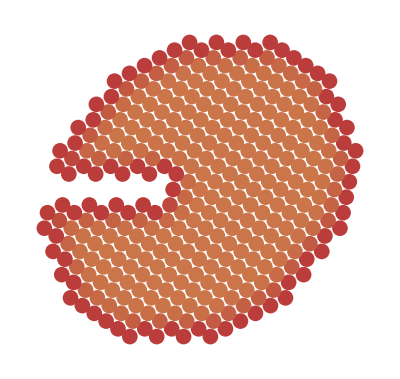

```mathematica
Block[{parts =DeleteCases[strainRelaxedParticles[10],{x_,y_}/;(-20< x < -2 && -.5 <y < .5)]
},
parts = ShearingTransform[0.2,{1,0},{0,1}][parts];
Graphics[particleGraphic[parts]]
]
```

```mathematica
Dynamic[{r,i,previousTime,time,iter,previousEnergy,totalEnergy}]
```

```mathematica
AbsoluteTiming[
Block[{positions =DeleteCases[strainRelaxedParticles[10],{x_,y_}/;(-4< x < -2 && -.1 <y < .1)]
,p,variables,startingPoint,iterations=0},
positions =  ShearingTransform[0.2,{1,0},{0,1}][positions];
variables=p[#]&/@Range[Length[positions]];
startingPoint = MapThread[{#1, #2}&,{variables,positions}];
iter = 0;
reapVals =Reap[{val,pos}=FindMinimum[wrapper[variables],startingPoint,
Method->"PrincipalAxis",MaxIterations->5000,StepMonitor:>( previousTime = time;
previousEnergy = totalEnergy;totalEnergy = wrapper[variables];
Sow[{totalEnergy,variables}];
iter++; time = DateString[])]
];
]
]
```

{4925.06,Null}

```mathematica
iterations = reapVals[[2,1]];
iterationEnergies = First/@iterations;
iterativePositions = Last/@iterations;
```

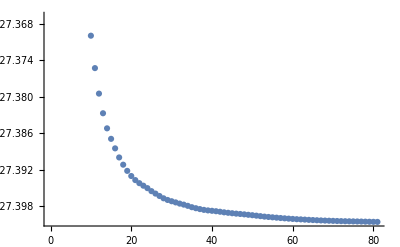

```mathematica
ListPlot[iterationEnergies]
```

```mathematica
Manipulate[
Graphics[particleGraphic[iterativePositions[[i]]]],
{i,1,Length[iterativePositions],1},
Dynamic[iterationEnergies[[i]]]
]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"iterations_r=10_big_internal_defect_iterationEnergies_iterativePositions.mx"}],{iterationEnergies,iterativePositions}];
```

```mathematica
AbsoluteTiming[
Block[{positions =Tuples[Range[-12,12],2],
,p,variables,startingPoint,iterations=0},
variables=p[#]&/@Range[Length[positions]];
startingPoint = MapThread[{#1, #2}&,{variables,positions}];
iter = 0;
reapValsSquare =Reap[{valSquare,posSquare}=FindMinimum[wrapper[variables],startingPoint,
Method->"PrincipalAxis",MaxIterations->5000,StepMonitor:>( previousTime = time;
previousEnergy = totalEnergy;totalEnergy = wrapper[variables];
Sow[{totalEnergy,variables}];
iter++; time = DateString[])]
];
]
]
```

```mathematica
iterationsSquare = reapValsSquare[[2,1]];
iterationEnergiesSquare = First/@iterationsSquare;
iterativePositionsSquare = Last/@iterationsSquare;
```

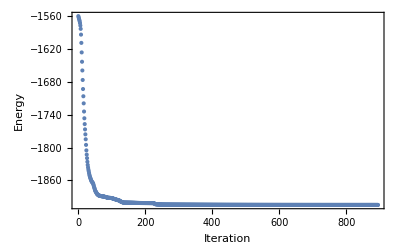

```mathematica
lpSquare = ListPlot[iterationEnergiesSquare, Frame->True, FrameLabel->{"Iteration","Energy"},(*PlotLabel->"Iterations during Minimization",*) BaseStyle->{FontSize->14},PlotRange->All]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"iterations_s=24_square_lattice_iterationEnergiesSquare_iterativePositionsSquare.mx"}],{iterationEnergiesSquare,iterativePositionsSquare,lpSquare}];
```

```mathematica
Manipulate[
GraphicsRow[{
Graphics[particleGraphic[iterativePositionsSquare[[i]]]],
Show[lpSquare, Graphics[{Red,PointSize[0.025],Point[{i,iterationEnergiesSquare[[i]]}]}]]
}
],
{i,1,Length[iterativePositionsSquare],1},
Dynamic[iterationEnergiesSquare[[i]]]
]
```

```mathematica
gamma[{nx_,ny_},α_]:= 1 + α(nx ny)^2
```

```mathematica
Manipulate[
ParametricPlot[gamma[AngleVector[θ],α]AngleVector[θ],{θ,0,2 π}],
{α,-3,3}
]
```

```mathematica
gamma[θ_,α_]:=gamma[AngleVector[θ],α];
```

```mathematica
Manipulate[
ParametricPlot[gamma[θ,α]AngleVector[θ],{θ,0,2 π}],
{α,-3,3}
]
```

```mathematica
Simplify[Simplify[FrenetSerretSystem[gamma[θ,α],θ],Assumptions->{α∈ Reals,0 < θ < 2 Pi}, Trig->False]/.{Cos[θ]->cosθ, Sin[θ]->sinθ}]
```

{{(2 (cosθ^4-6 cosθ^2 sinθ^2+sinθ^4) α)/((1+(2 cosθ^3 sinθ α-2 cosθ sinθ^3 α)^2)^(3/2))},{{1/(√(1+(2 cosθ^3 sinθ α-2 cosθ sinθ^3 α)^2)),(2 cosθ sinθ (cosθ^2-sinθ^2) α)/(√(1+(2 cosθ^3 sinθ α-2 cosθ sinθ^3 α)^2))},{(2 cosθ sinθ (-cosθ^2+sinθ^2) α)/(√(1+(2 cosθ^3 sinθ α-2 cosθ sinθ^3 α)^2)),1/(√(1+(2 cosθ^3 sinθ α-2 cosθ sinθ^3 α)^2))}}}

```mathematica
√(1+(2 nx^3 ny α-2 nx ny^3 α)^2){{1/(√(1+(2 nx^3 ny α-2 nx ny^3 α)^2)),(2 nx ny (nx^2-ny^2) α)/(√(1+(2 nx^3 ny α-2 nx ny^3 α)^2))},{(2 nx ny (-nx^2+ny^2) α)/(√(1+(2 nx^3 ny α-2 nx ny^3 α)^2)),1/(√(1+(2 nx^3 ny α-2 nx ny^3 α)^2))}}
```

{{1,2 nx ny (nx^2-ny^2) α},{2 nx ny (-nx^2+ny^2) α,1}}

```mathematica
herringTangentCircle[{nx_,ny_},α_]:= 
Block[{curvature,tangent,normal, center, radius,t} ,
denom = √(1+(2 nx^3 ny α-2 nx ny^3 α)^2);
{{curvature},{tangent, normal}}= FrenetSerretSystem[gamma[t,α],t]/.t->θ;

(*=1/denom{
{(2 (nx^4-6 nx^2 ny^2+ny^4) α)/denom^2},{{1,del},{-del ,1}}}*);
If[PossibleZeroQ[curvature],radius = 10^12,radius = 1/curvature];
center =gamma[{nx,ny},α] + normal radius;
Circle[center, Abs@radius]
]
```

```mathematica
Simplify[D[gamma[AngleVector[θ],α]AngleVector[θ],θ]]
```

{Sin[θ] (-1+2 α Cos[θ]^4-3 α Cos[θ]^2 Sin[θ]^2),Cos[θ] (1+3 α Cos[θ]^2 Sin[θ]^2-2 α Sin[θ]^4)}

```mathematica
Simplify[Sqrt[Simplify[D[gamma[AngleVector[θ],α]AngleVector[θ],θ]].Simplify[D[gamma[AngleVector[θ],α]AngleVector[θ],θ]]], Trig->False]
```

√(Sin[θ]^2 (1-2 α Cos[θ]^4+3 α Cos[θ]^2 Sin[θ]^2)^2+Cos[θ]^2 (1+3 α Cos[θ]^2 Sin[θ]^2-2 α Sin[θ]^4)^2)

```mathematica
unitTangent[θ_,α_]:= {Sin[θ] (-1+2 α Cos[θ]^4-3 α Cos[θ]^2 Sin[θ]^2),Cos[θ] (1+3 α Cos[θ]^2 Sin[θ]^2-2 α Sin[θ]^4)}/(√(Sin[θ]^2 (1-2 α Cos[θ]^4+3 α Cos[θ]^2 Sin[θ]^2)^2+Cos[θ]^2 (1+3 α Cos[θ]^2 Sin[θ]^2-2 α Sin[θ]^4)^2))
```

```mathematica
herringTangentCircle[θ_,α_]:= 
Block[{ϕ,normalToCurve,tangentToCurve, center, radius,gamMag} ,
tangentToCurve=unitTangent[θ,α];
normalToCurve ={-1,1}Reverse[tangentToCurve];
ϕ= ArcTan@@normalToCurve;
gamMag= gamma[θ,α];
radius =(gamMag/2)/Cos[Pi -ϕ + θ];
center = gamMag AngleVector[θ] +radius normalToCurve;

Circle[center, Abs@radius]]
```

```mathematica
Expand[(-1+(2-7 ny^2+5 ny^4) α)]
```

-1+2 α-7 ny^2 α+5 ny^4 α

```mathematica
tmp/.
```

```mathematica
Clear[phi]
```

```mathematica
normalTangent[{nx_,ny_},α_]:= With[{denom =√(1+30 ny^6 α^2-15 ny^8 α^2+2 ny^2 α (1+2 α)-ny^4 α (2+19 α)) },
{nx,ny}{(-1+(2-7 ny^2+5 ny^4) α),(1+3 ny^2 α-5 ny^4 α)}/denom
]
```

```mathematica
(*herringTangentCircle[{nx_,ny_},α_]:= 
Block[{normalTangent = normalTangent[{nx,ny},α], ϕ, radius, 
θ= ArcTan@@{nx,ny},
gammaMag=gamma[{nx,ny},α] ,
center},
ϕ = ArcTan@@normalTangent;
radius = gammaMag/Cos[θ+ϕ - Pi/2];
center =  gammaMag AngleVector[θ] + radius AngleVector[ϕ - Pi/2];
Circle[center, Abs@radius]
]*)
```

```mathematica
herringTangentCircle[.1,.2]
```

Circle[{0.896115,3.72035},2.72044]

```mathematica
Manipulate[
Graphics[
herringTangentCircle[θ,α]
],
{θ,0,2Pi},
{α,-5,5}
]
```

```mathematica
With[{gammaPlot =ParametricPlot[gamma[AngleVector[θ],α]AngleVector[θ],{θ,0,2 π}]
},
Manipulate[
Show[
ParametricPlot[gamma[AngleVector[theta],α]AngleVector[theta],{theta,0,2 π}],
Graphics[
{Point[gamma[AngleVector[θ],α]AngleVector[θ]],herringTangentCircle[θ,α],
InfiniteLine[gamma[AngleVector[θ],α]AngleVector[θ],
{-1,1}Reverse[gamma[AngleVector[θ],α]AngleVector[θ]]],
Arrow[{{0,0},gamma[AngleVector[θ],α]AngleVector[θ]}]}
]
]
,
{α,-3,3},
{θ,0,2 Pi}
]
]
```

```mathematica
With[{gammaPlot =ParametricPlot[gamma[AngleVector[θ],α]AngleVector[θ],{θ,0,2 π}]
},
Manipulate[
Show[
ParametricPlot[gamma[AngleVector[theta],α]AngleVector[theta],{theta,0,2 π}],
Graphics[
{Point[gamma[AngleVector[θ],α]AngleVector[θ]],herringTangentCircle[θ,α],
Arrow[{{0,0},gamma[AngleVector[θ],α]AngleVector[θ]}],

}
]
]
,
{α,-3,3},
{θ,0,2 Pi}
]
]
```